```mathematica
GetIdFromGraph[g_]:=Block[{vertices=VertexList[g]},
FromDigits[
Flatten[
Table[
Table[
If[EdgeQ[g,vertices[[ i]]<->vertices[[ j]] ],1,0]
,
{j,i+1, VertexCount[g]}
],
{i,1, VertexCount[g]}
]
],
3]
]
```

```mathematica
GetIdFromGraph[allGraphs5[lambdaKey,"graph"]]
```

20665

```mathematica
lambdaKey
```

20665

```mathematica
EmbedGraph[master_,key_,vertices_]:=Block[
{val=allGraphs5[key], sets, reference=vertices, g, sub, edge},
sets=val["vertexsets"];
g=master;
(* delete existing edges *)
Table[
Table[
edge=vertices[[i]]<->vertices[[j]];
If[EdgeQ[g,edge],
g = EdgeDelete[g,edge]
]
,{j,i+1,5}
]
,{i,1,5}
];
(* contract vertices if needed *)
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];

sub=val["graph"];
(* add edges *)
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}
];
g
]
```

```mathematica
ShowGraph5Least[36898]
```

-Graphics-368980

```mathematica
EmbedGraph[-Graphics-,36898,{5,2,4,3,1}]
```

-Graphics-

```mathematica
Monitor[Table[allGraphs2[k,"chromial"]=ChromaticPolynomial[allGraphs2[k,"graph"],x],{k,Keys[allGraphs2]}],k];
```

```mathematica
Monitor[Table[allGraphs3[k,"chromial"]=ChromaticPolynomial[allGraphs3[k,"graph"],x],{k,Keys[allGraphs3]}],k];
```

```mathematica
Monitor[Table[allGraphs4[k,"chromial"]=ChromaticPolynomial[allGraphs4[k,"graph"],x],{k,Keys[allGraphs4]}],k];
```

```mathematica
Monitor[Table[allGraphs5[k,"chromial"]=ChromaticPolynomial[allGraphs5[k,"graph"],x],{k,Keys[allGraphs5]}],k];
```

```mathematica
Clear[CalcChromial];
```

```mathematica
CalcChromialBig[g_,pos_:""]:=Block[{vertices, subGraph,id,index,prefix,h,subresult,fulls,nexts},
If[pos=="",prefix="",prefix=ToString[pos]<>"."];
id=K5Key;
While[id==K5Key,
vertices = VertexList[g];
vertices=RandomSample[vertices,5];
subGraph=Subgraph[g,vertices];
id = GetIdFromGraph[subGraph];
];
index=0;
fulls=(ListofVars[allGraphs5[id,"colofour"]]/.RepKey["C"]);
Total[
Table[
h=EmbedGraph[g,fullId,vertices];
subresult=CalcChromial[h,prefix<>ToString[index++]];
(*Print[ {Graph[g,VertexLabels->"Name",ImageSize->80],prefix<>ToString[index]->ShowGraph5Least[fullId],vertices,Factor[subresult],Graph[h,VertexLabels->"Name",ImageSize->80],Factor[ ChromaticPolynomial[h,x]]}];*)
subresult
,
{fullId,fulls}
]
]
]
```

```mathematica
CalcChromial[g_,pos_:""]:=Block[{vertices, subGraph,id,index,prefix,h,subresult},
If[pos=="",prefix="",prefix=ToString[pos]<>"."];
If[CompleteGraphQ[g]||EmptyGraphQ[g], 
ChromaticPolynomial[g,x]
,
If[VertexCount[g]<=5,
id = GetIdFromGraph[g];
If[VertexCount[g]==1,x
,
If[VertexCount[g]==2,allGraphs2[id,"chromial"]
,
If[VertexCount[g]==3,allGraphs3[id,"chromial"]
,
If[VertexCount[g]==4,
allGraphs4[id,"chromial"]
,
allGraphs5[id,"chromial"]
]
]
]
]
,
CalcChromialBig[g,pos]
]
]
]
```

```mathematica
GetIdFromGraph[CycleGraph[4]]
```

280

```mathematica
CalcChromial[CycleGraph[4]]//Timing
```

{4,280}

{0.,Null (-3 x+6 x^2-4 x^3+x^4)}

```mathematica
ChromaticPolynomial[CycleGraph[4],x]//CompleteBaseCoeff//Timing
```

{0.,{0,0,1,2,1}}

```mathematica
Table[CalcChromial[CycleGraph[kk],""],{kk,6}]
```

{x,-x+x^2,2 x-3 x^2+x^3,-3 x+6 x^2-4 x^3+x^4,4 x-10 x^2+10 x^3-5 x^4+x^5,-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6}

```mathematica
Table[ShowGraph5Least[k],{k,{51478,51475,49963,49210,49207,36898,36817,36166,36112,36085,31738,31714,31711,30334,30253,29608,29605,29551,29527,29524}}]
```

{-Graphics-514780,-Graphics-514750,-Graphics-499631,-Graphics-492100,-Graphics-492070,-Graphics-368980,-Graphics-368170,-Graphics-361660,-Graphics-361120,-Graphics-360850,-Graphics-317380,-Graphics-317140,-Graphics-317110,-Graphics-303340,-Graphics-302530,-Graphics-296080,-Graphics-296050,-Graphics-295510,-Graphics-295270,-Graphics-295240}

```mathematica
EmptyGraphQ
```

```mathematica
Keys[allGraphs4[280]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull}

```mathematica
allGraphs4[280,"graph"]
```

-Graphics-

```mathematica
GetIdFromGraph[-Graphics-]
```

4

```mathematica
Table[CalcChromial[CycleGraph[k]]//Timing,{k,1,9 }]
```

{{0.,x},{0.,-x+x^2},{0.,2 x-3 x^2+x^3},{0.,-3 x+6 x^2-4 x^3+x^4},{0.,4 x-10 x^2+10 x^3-5 x^4+x^5},{0.015625,-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6},{0.09375,6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7},{0.765625,-7 x+28 x^2-56 x^3+70 x^4-56 x^5+28 x^6-8 x^7+x^8},{6.25,8 x-36 x^2+84 x^3-126 x^4+126 x^5-84 x^6+36 x^7-9 x^8+x^9}}

```mathematica
Table[ChromaticPolynomial[CycleGraph[k],x]//Timing,{k,1,24 }]
```

{{0.,0},{0.,-x+x^2},{0.015625,2 x-3 x^2+x^3},{0.,-3 x+6 x^2-4 x^3+x^4},{0.,4 x-10 x^2+10 x^3-5 x^4+x^5},{0.,-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6},{0.,6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7},{0.,-7 x+28 x^2-56 x^3+70 x^4-56 x^5+28 x^6-8 x^7+x^8},{0.,8 x-36 x^2+84 x^3-126 x^4+126 x^5-84 x^6+36 x^7-9 x^8+x^9},{0.,-9 x+45 x^2-120 x^3+210 x^4-252 x^5+210 x^6-120 x^7+45 x^8-10 x^9+x^10},{0.,10 x-55 x^2+165 x^3-330 x^4+462 x^5-462 x^6+330 x^7-165 x^8+55 x^9-11 x^10+x^11},{0.,-11 x+66 x^2-220 x^3+495 x^4-792 x^5+924 x^6-792 x^7+495 x^8-220 x^9+66 x^10-12 x^11+x^12},{0.,12 x-78 x^2+286 x^3-715 x^4+1287 x^5-1716 x^6+1716 x^7-1287 x^8+715 x^9-286 x^10+78 x^11-13 x^12+x^13},{0.,-13 x+91 x^2-364 x^3+1001 x^4-2002 x^5+3003 x^6-3432 x^7+3003 x^8-2002 x^9+1001 x^10-364 x^11+91 x^12-14 x^13+x^14},{0.,14 x-105 x^2+455 x^3-1365 x^4+3003 x^5-5005 x^6+6435 x^7-6435 x^8+5005 x^9-3003 x^10+1365 x^11-455 x^12+105 x^13-15 x^14+x^15},{0.,-15 x+120 x^2-560 x^3+1820 x^4-4368 x^5+8008 x^6-11440 x^7+12870 x^8-11440 x^9+8008 x^10-4368 x^11+1820 x^12-560 x^13+120 x^14-16 x^15+x^16},{0.,16 x-136 x^2+680 x^3-2380 x^4+6188 x^5-12376 x^6+19448 x^7-24310 x^8+24310 x^9-19448 x^10+12376 x^11-6188 x^12+2380 x^13-680 x^14+136 x^15-17 x^16+x^17},{0.,-17 x+153 x^2-816 x^3+3060 x^4-8568 x^5+18564 x^6-31824 x^7+43758 x^8-48620 x^9+43758 x^10-31824 x^11+18564 x^12-8568 x^13+3060 x^14-816 x^15+153 x^16-18 x^17+x^18},{0.,18 x-171 x^2+969 x^3-3876 x^4+11628 x^5-27132 x^6+50388 x^7-75582 x^8+92378 x^9-92378 x^10+75582 x^11-50388 x^12+27132 x^13-11628 x^14+3876 x^15-969 x^16+171 x^17-19 x^18+x^19},{0.,-19 x+190 x^2-1140 x^3+4845 x^4-15504 x^5+38760 x^6-77520 x^7+125970 x^8-167960 x^9+184756 x^10-167960 x^11+125970 x^12-77520 x^13+38760 x^14-15504 x^15+4845 x^16-1140 x^17+190 x^18-20 x^19+x^20},{0.,20 x-210 x^2+1330 x^3-5985 x^4+20349 x^5-54264 x^6+116280 x^7-203490 x^8+293930 x^9-352716 x^10+352716 x^11-293930 x^12+203490 x^13-116280 x^14+54264 x^15-20349 x^16+5985 x^17-1330 x^18+210 x^19-21 x^20+x^21},{0.,-21 x+231 x^2-1540 x^3+7315 x^4-26334 x^5+74613 x^6-170544 x^7+319770 x^8-497420 x^9+646646 x^10-705432 x^11+646646 x^12-497420 x^13+319770 x^14-170544 x^15+74613 x^16-26334 x^17+7315 x^18-1540 x^19+231 x^20-22 x^21+x^22},{0.,22 x-253 x^2+1771 x^3-8855 x^4+33649 x^5-100947 x^6+245157 x^7-490314 x^8+817190 x^9-1144066 x^10+1352078 x^11-1352078 x^12+1144066 x^13-817190 x^14+490314 x^15-245157 x^16+100947 x^17-33649 x^18+8855 x^19-1771 x^20+253 x^21-23 x^22+x^23},{0.,-23 x+276 x^2-2024 x^3+10626 x^4-42504 x^5+134596 x^6-346104 x^7+735471 x^8-1307504 x^9+1961256 x^10-2496144 x^11+2704156 x^12-2496144 x^13+1961256 x^14-1307504 x^15+735471 x^16-346104 x^17+134596 x^18-42504 x^19+10626 x^20-2024 x^21+276 x^22-24 x^23+x^24}}

```mathematica
ChromaticPolynomial[CycleGraph[20],x]//Timing
```

{0.,-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6}

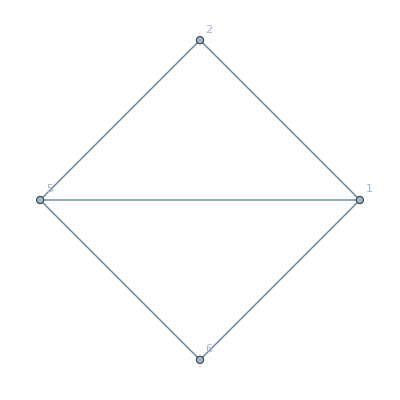

```mathematica
Graph[EmbedGraph[CycleGraph[6],alfa1Key,{1,2,3,4,5}], VertexLabels->"Name"]
```